## Generowanie funkcji G(x,y) określającej współczynnik rozpylenia dla punktu (x,y)

Jestem przyzwyczajony do używania znaków ⟦ i ⟧ zamiast [[ i ]], jest to dla mnie czytelniejsze. Wpisuje się je klawiszami escape [[ escape oraz escape ]] escape.

## Wartości stałe

### Rozmiar próbki (200nm x 200nm)

```mathematica
size=500;
```

```mathematica
fileSize=500;
```

### Liczba punktów będących zarodkami polikryształów

```mathematica
n=Ceiling[220*size*size/(200*200)]
```

55

```mathematica
n
```

55

```mathematica
(* maksymalna liczba kroków *)
(*accuracy=80;*)
accuracy=20;
```

```mathematica
precision=10;
```

```mathematica
workingPrecision=17;
```

```mathematica
minPoints=1(*IntegerPart[0.99*size]*)
```

1

```mathematica
maxPoints=1000;
```

```mathematica
nomAngleInDegrees=70;
```

### Minimalna i maksymalna wartość współczynnika rozpylania

```mathematica
minSputter=0.7;
```

```mathematica
maxSputter = 1.2;
```

#### Kąt padania jonów

```mathematica
nomAngle=80°
```

80 °

### Czas trwania

```mathematica
dose=185;
```

```mathematica
(* 60s *)
```

```mathematica
tMax=dose/1.7*1000000
```

1.08824×10^8

## Stworzenie tablicy G

Tu pobawiłem się trochę obsługą plików. Najpierw ustawiam ścieżkę obsługi plików z jakiejś domyślnej na tą gdzie znajduje się ten notebook. Potem jest zwykły if, w którym sprawdzam czy w tym folderze istnieje plik g_raw.dat i zmienna importGQ (czy chcę importować G z pliku) jest równa True. Jeśli tak to go importuję. Jeśli nie to otwieram plik erosion_G_new.nb (nie wiem czemu tutaj nie działa ścieżka ustawiona w SetDirectory dlatego cała konstrukcja z FileNameJoin), wykonuję go w całości i jak się wykona zamykam bez zapisu (dzięki temu outputy w pliku pierwotnym nie zmienią się).

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\lukasz\Dropbox\dissertation\ripple-formation\mathematica

```mathematica
importGQ=True;
```

```mathematica
If[
FileExistsQ[StringJoin["data/g_raw_", ToString[fileSize],".dat"]]
&&FileExistsQ[StringJoin["data/seeds_",ToString[fileSize],".dat"]]
&&FileExistsQ[StringJoin["data/sputter_coeffs_",ToString[fileSize], ".dat"]]
&&importGQ,

G=Import[StringJoin["data/g_raw_", ToString[fileSize],".dat"],"Table"];seeds=Import[StringJoin["data/seeds_",ToString[fileSize],".dat"]]; sputterCoeffs=Import[StringJoin["data/sputter_coeffs_",ToString[fileSize], ".dat"]];,

notebookG=NotebookOpen[FileNameJoin[{NotebookDirectory[],"prepare_data.nb"}]];
NotebookEvaluate[notebookG,InsertResults->True];
NotebookClose[notebookG];
]
```

## Dalsze obliczenia

### Przypisanie do poszczególnych krystalitów ich współczynników rozpylania

Używasz (szczególnie w obliczeniach G, które dałem do osobnego pliku) konstrukcji For, które nie są w Mathematice najwydajniejsze. Wszędzie tam gdzie chodzisz po liście można to zrobić funkcją Table, która jest dużo szybsza. Przepisałem twoje konstrukcje tak, żeby używały Table zapisując wyniki w zmiennych z dopisanym “2”. Żeby pokazać ci jakie są różnice w czasie wykonywania obu typów konstrukcji objąłem je funkcją AbsoluteTiming, która zwraca czas wykonywania instrukcji (całkowity, łącznie z czasem jaki jest potrzebny na wyświetlenie wyników, itp.).

```mathematica
G2=G;
```

```mathematica
AbsoluteTiming[
For[i=1,i≤size+1,++i,
For[j=1,j≤size+1,++j,
G[[i,j]]=sputterCoeffs[[G[[i,j]]]][[1]]
(* Random sputter coeffs *)
(*G[[i,j]]=sputterCoeffs[[G[[i,j]]]][[1]]*)
(* Test 1 *)
(* All the same sputter coeff 1.0 *)
(*G[[i,j]]=1.0*)
(* Test 2 *)
(* Two sputter coeffs 0.7 and 1.2 *)
(*G[[i,j]]=If[i≤size/2,0.7,1.2]*)
]
]
]
```

{0.0542019,Null}

```mathematica
i=.
j=.
k=.
```

```mathematica
(*AbsoluteTiming[
G2=Table[sputterCoeffs⟦G2⟦i,j⟧⟧,{i,size+1},{j,size+1}];
]*)
```

Zamiast Rotate wpisałem Reverse i Transpose czyli zamiast obracać obrazek (i przy okazji wszystkie osie, legendy, itp.) obróciłem dane.

```mathematica
G;
```

```mathematica
G[[1;;size,1;;size]];
```

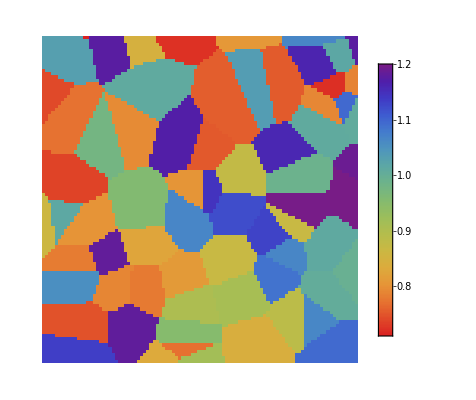

```mathematica
ArrayPlot[Reverse[Transpose[G[[1;;size,1;;size]]]], ColorFunction->(ColorData["Rainbow"][1-#]&), PlotLegends->Automatic]
```

Tutaj było clue problemu. Niestety Part (czyli ⟦ ⟧) nie może być wykonane jeśli indeksy nie są numeryczne. W Mathematice 10 wprowadzono funkcję Indexed, która robi dokładnie to co jest potrzebne czyli wyciąga coś z listy jeśli ma podane indeksy numeryczne a jak indeksy są symboliczne to pozostaje w formie abstrakcyjnej (symbolicznej). Jeśli chciałbyś mieć funkcję, która będzie działała we wcześniejszych wersjach to działać powinno rozwiązanie wykomentowane poniżej.

```mathematica
(*ListPart[x_List,spec__]:=x[[spec]];
Gfun2Old[x_,y_,t_]:=ListPart[G,Floor[x+1],Floor[y+1]]*)
```

```mathematica
(*mając tablicę G tworzę funkcję zwracającą wartość G dla pary(x,y)*)
Gfun[xparam_,yparam_,tparam_]:=G⟦Floor[xparam+1],Floor[yparam+1]⟧
```

```mathematica
Gfun2[xparam_,yparam_,tparam_]:=Indexed[G,{Floor[xparam+1],Floor[yparam+1]}]
```

```mathematica
Indexed[G,{Floor[2],Floor[3]}]
```

1.13474

### Ten sam rysunek (z użyciem tych samych zarodków ziaren, bez kolorowania) z użyciem VoronoiMesh - funkcji wbudowanej w Mathematicę

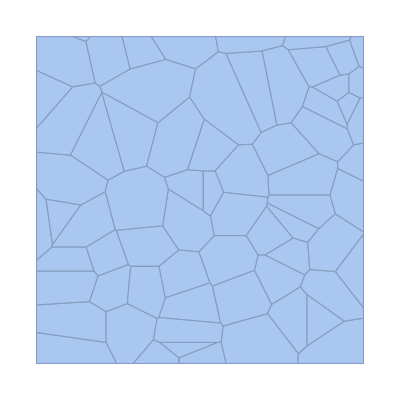

```mathematica
vor = VoronoiMesh[seeds, {{0, size+1}, {0,size+1}}]
```

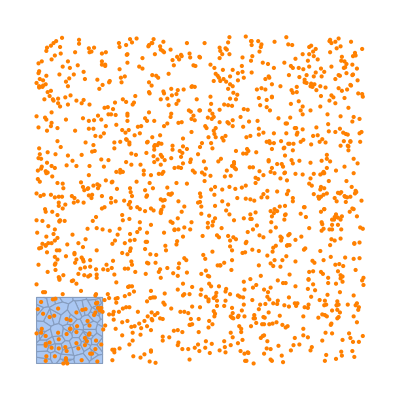

```mathematica
Show[%, Graphics[{Orange, Point[seeds]}]]
```

```mathematica
cells=MeshPrimitives[vor,2];
```

### Funkcja Yammamury

```mathematica
(* bierze pod uwagę zmianę współczynnika rozpylania spowodowaną zmianą lokalnego kąta padania strumienia *)
```

```mathematica
Y0=33/10; (* atom/jon współczynnik rozpylania dla strumienia padającego pod kątem prostym *)
```

```mathematica
f=195/100; (* bezwymiarowy współczynnik opisujący kształt zależności kątowej *)
```

#### Kąt dla którego współczynnik rozpylania jest największy

```mathematica
thOpt=70 * Pi/180
```

(7 π)/18

```mathematica
thOpt=70°
```

70 °

#### Definicja funkcji Yammamury

```mathematica
yammFormula[th_]:=Y0*Cos[th]^-f*Exp[f*(1-Cos[th]^-1)*Cos[thOpt]]
```

```mathematica
(* test funkcji Yammamury dla kątów od 0° do 90° *)
```

Wszystkie opisy osi, jeśli nie mają być pod nie podstawione zmienne, lepiej jest, żeby były wpisane jako string czyli otoczone cudzysłowami.

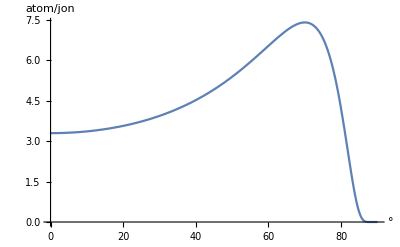

```mathematica
Plot[yammFormula[th Degree], {th,0,90},AxesLabel->{"°","atom/jon"}]
```

### Funkcja odpowiadająca za erozję powierzchni

```mathematica
Clear[h]
```

```mathematica
(* objętość atomu niklu *)
```

```mathematica
omega=1/(917/10);
```

```mathematica
(* strumień jonów *)
```

```mathematica
phi=7946/1000000000;
```

```mathematica
(* funkcja opisująca zależność cosinus lokalnego kąta padania od nominalnego kąta padania *)
```

Jako argument przekazujesz tylko nazwę funkcji, bez jej parametrów. Jeśli musiałbyś przekazać też bezpośrednio argumenty funkcji h to powinieneś je dodać jako zwykłe argumenty. Za to w samej funkcji zrobiłeś właściwie czyli musisz podać bezpośrednio wszystkie argumenty dla funkcji h.

```mathematica
cosThLocFormula[h_,x_,y_,t_,thNom_]:=(Sin[thNom]*D[h[x,y,t],x]+Cos[thNom])/Sqrt[D[h[x,y,t],y]^2+1+D[h[x,y,t],x]^2]
```

```mathematica
(* funkcja opisująca cosinus kąta pomiędzy normalną do lokalnej płaszczyzny a normalną do średniej płaszczyzny *)
```

```mathematica
cosThOffFormula[h_,x_,y_,t_]:=1/Sqrt[D[h[x,y,t],y]^2+1+D[h[x,y,t],x]^2]
```

```mathematica
EFormula[h_,x_,y_,t_,thNom_]:=-omega*phi*cosThLocFormula[h,x,y,t,thNom]/cosThOffFormula[h,x,y,t]*yammFormula[ArcCos[cosThLocFormula[h,x,y,t, thNom]]]*Gfun2[x,y,t]
```

### Równanie ewolucji powierzchni

```mathematica
Clear[x]
```

```mathematica
Clear[y]
```

```mathematica
Clear[t]
```

```mathematica
nomAngle
```

80 °

```mathematica
pde=D[h[x,y,t],t]==EFormula[h, x,y,t,nomAngle];
```

```mathematica
BConds = {h[0,y,t]==h[size,y,t],h[x,0,t]==h[x,size,t]}
```

{h[0,y,t]==h[100,y,t],h[x,0,t]==h[x,100,t]}

```mathematica
(* stożek??? *)
```

```mathematica
topographySimple[x1_,x2_]=If[x1≤size/4 , 0, If[x1<size/2,(400/size*x1-100),If[x1<3*size/4, (300-400/size*x1), 0]]]
```

If[x1≤25,0,If[x1<size/2,(400 x1)/size-100,If[x1<(3 size)/4,300-(400 x1)/size,0]]]

Zamiast takiego If można w Mathematice użyć Piecewise, które powinno działać razem z większą ilością funkcji i jest trochę czytelniejsze.

```mathematica
(* Niepłaska powierzchnia początkowa *)
```

```mathematica
size
```

100

```mathematica
topography[x1_,x2_]=Piecewise[{{(400/size*x1-100),size/4<x1<size/2},{(300-400/size*x1),size/2<x1<3*size/4},{100, x1==size/2},{0, x1≤size/4},{0, x1≥3*size/4}}];
```

```mathematica
topographyAlongY[x1_,x2_]=Piecewise[{{(400/size*x2-100),size/4<x2<size/2},{(300-400/size*x2),size/2<x2<3*size/4},{100, x2==size/2},{0, x2≤size/4},{0, x2≥3*size/4}}];
```

```mathematica
(*(*topography[x,y]*) (*400-400/199*x*)*)
```

```mathematica
(*ICond=h[x,y,0]==topographyAlongY[x,y];*)
```

```mathematica
(*ICond=h[x,y,0]==topography[x,y];*)
```

```mathematica
(*Płaska powierzchnia początkowa *)
```

```mathematica
ICond=h[x,y,0]==0;
```

```mathematica
size
```

100

```mathematica
(*sol=NDSolve[Join[{pde},BConds,{ICond}],h,{x,0,size},{y,0,size},{t,0,tMax},AccuracyGoal->10,PrecisionGoal->10,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->100}}]*)
```

```mathematica
sol=NDSolve[Join[{pde},BConds,{ICond}],h,{x,0,size},{y,0,size},{t,0,tMax},AccuracyGoal->accuracy,PrecisionGoal->precision,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->minPoints,"MaxPoints"->maxPoints}},WorkingPrecision->workingPrecision,InterpolationOrder->All]
```

{{h→                                                                                                              8
InterpolatingFunction[{{…, 0, 100.00000000000000, …}, {…, 0, 100.00000000000000, …}, {0, 1.0882352941176471 10 }}, <>]}}

```mathematica
(*sol=NDSolve[Join[{pde},BConds,{ICond}],h,{x,0,size},{y,0,size},{t,0,tMax}];*)
```

```mathematica
(*sol=NDSolve[Join[{pde},BConds,{ICond}],h,{x,0,size},{y,0,size},{t,0,tMax}]*)
```

```mathematica
IntegerPart[0.9*size]
```

90

```mathematica
ffun[x_,y_,t_]:=h[x,y,t]/.sol⟦1⟧
```

```mathematica
ffun[150,150,1000000]
```

-0.05069964140521415

```mathematica
Manipulate[ContourPlot[ffun[x,y,t],{x,0,size},{y,0,size},ColorFunction->(ColorData["Rainbow"][1#]&), PlotLegends->Automatic],{t,0,tMax}]
```

```mathematica
tMax
```

1.08824×10^8

```mathematica
Plot3D[Evaluate@Table[ffun[x,y,t], {t,{tMax}}],{x,0,size},{y,0,size},ColorFunction->"Rainbow",PlotLegends->Automatic, AxesLabel->{"nm","nm","nm"}]
```

-Graphics3D-

```mathematica
(*Wykres dla czasu t=0 (czerwony) i dla czasu t=tMax (zielony) *)
```

```mathematica
Manipulate[Plot3D[Evaluate@Table[ffun[x,y,t], {t,{time,tMax}}],{x,0,size},{y,0,size},PlotStyle->{Red,Green},PlotLegends->Automatic,AxesLabel->{"nm","nm","nm"},PlotRange->{{0,size},{0,size},{-20,100}}],{time,0,tMax}]
```